### Predict

Predict is a function that works on variety of data types and output a PredictorFunction. It predicts a value from the given data. The format for data is rule based array {data -> target}. The target need to be a numerical value. It automatically selects a machine learning model based on the type of data. But we can also specify method of our own choosing using Method->” “.

```mathematica
pd = Predict[{1.11->1,2.22->2,3.33->3,4.44->4,4.44->5}]
```

PredictorFunction[…]

```mathematica
pd[3.7]
```

3.61515

Getting the Regression line.

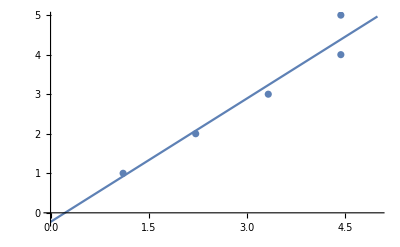

```mathematica
Show[Plot[pd[x],{x,0,5},Exclusions->None],ListPlot[List@@@{1.11->1,2.22->2,3.33->3,4.44->4,4.44->5}]]
```

We can also get information about PredictorFunction, just as we did in classify.

```mathematica
PredictorInformation[pd]
```

Predictor information
Method | Linear regression
Number of features | 1
Number of training examples | 5
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1

Let’s choose a dataset.

```mathematica
ExampleData["MachineLearning"]
```

{{MachineLearning,BostonHomes},{MachineLearning,FisherIris},{MachineLearning,MNIST},{MachineLearning,MovieReview},{MachineLearning,Mushroom},{MachineLearning,Satellite},{MachineLearning,Titanic},{MachineLearning,UCILetter},{MachineLearning,WineQuality}}

```mathematica
boston = ExampleData[{"MachineLearning","BostonHomes"},"TrainingData"];
```

```mathematica
boston[[1]]
```

{0.02731,0,7.07,0,0.469,6.421,78.9,4.9671,2,242,17.8,396.9,9.14}→21.6

```mathematica
bostonpd = Predict[boston]
```

PredictorFunction[…]

```mathematica
PredictorInformation[bostonpd]
```

Predictor information
Method | Random forest
Number of features | 1
Number of training examples | 338
Number of trees | 10

```mathematica
bostonpd[{0.0324,19,3.22,0.3,0.563,2.354,70.0,5.03,0.5,284,14.3,234.5,3.09}]
```

26.6268